```mathematica
Clear["Global`*"]
```

```mathematica
a=2.46;(*a is given in units of 10^-10*)
γ0=3.1;
γ1=0.38;
γ2=-0.015;
γ3=0.29;
γ4=0.141;
δ=-0.0105;
Δ1=0.05;
Δ2=-0.0023;
(*γ1=0.;
γ2=0.;
γ3=0.;
γ4=0.;
δ=0.;
Δ1=0.;
Δ2=0.;*)
u[kx_,ky_]=1.+2.*Cos[0.5*kx*a]*Exp[-ⅈ*ky*a*0.5*√3];
v[kx_,ky_]=Exp[ⅈ*ky*a*√3]*u[kx,ky];
Hk[kx_,ky_]={{Δ1+Δ2,-γ0*u[kx,ky],γ4*u[kx,ky]*,γ1,0,0},{-γ0*u[kx,ky]*,Δ1+Δ2+δ,γ3*v[kx,ky],γ4*u[kx,ky]*,0.5*γ2,0},{γ4*u[kx,ky],γ3*v[kx,ky]*,-2.*Δ2,-γ0*u[kx,ky],γ4*v[kx,ky]*,γ1},{γ1,γ4*u[kx,ky],-γ0*u[kx,ky]*,-2.*Δ2,γ3*u[kx,ky],γ4*u[kx,ky]*},{0,0.5*γ2,γ4*v[kx,ky],γ3*u[kx,ky]*,Δ2-Δ1+δ,-γ0*v[kx,ky]},{0,0,γ1,γ4*u[kx,ky],-γ0*v[kx,ky]*,Δ2-Δ1}};
(*Number of bands*)
Nb=Length[Hk[kx,ky]];
```

```mathematica
μ=-0.049;(*0.065*γ0;Chemical potential. VHS is at μ=-0.052175;*)
kbT=0.0000861*1; (*Boltzmann's k × temperature*)
η=0.000001;(*Self energy*) 
δc=10.*kbT;
FDif[ϵk_]=If[Abs[μ-ϵk]<δc,1/(1+Exp[(ϵk-μ)/kbT]),UnitStep[μ-ϵk]];
δFif[ϵk_]=If[Abs[μ-ϵk]<δc,-1./kbT/(2*(1+Cosh[(ϵk-μ)/kbT])),0.];
```

```mathematica
Nk=50;(*k-mesh will have Nk^2 points, Nk>1, integer*)
StringForm["The k-mesh has `` points.",Nk^2]
Λk=1; (*A factor controlling the size of the mesh in k space*)
Δk=Λk/Nk; (*Spacing between k-points*)

b=(4π)/(√3*a); (*Magnitude of reciprocal vectors*)
b1=b*{(-√3)/2,1/2}; (*Reciprocal vectors b1,b2*)
b2=b*{(√3)/2,1/2};
lineb1=Arrow[{{0,0},b1}]; 
lineb2=Arrow[{{0,0},b2}]; 
BZcontour = Polygon[{((4π)/(3a))*{-1,0},((4π)/(3a))*{(-1)/2,(√3)/2},((4π)/(3a))*{1/2,(√3)/2},((4π)/(3a))*{1,0},((4π)/(3a))*{1/2,(-√3)/2},((4π)/(3a))*{(-1)/2,(-√3)/2}}];
kaMesh=Flatten[Table[{(j-i)*Δk*b*((√3)/2),(j+i)*Δk*b*(1/2)},{i,1,Nk,1},{j,1,Nk,1}],1]; (*k-mesh first generated by reciprocal vectors *)
kaMesh1BZ=kaMesh-TensorProduct[(1-UnitStep[kaMesh.b2])*UnitStep[kaMesh.(b1+b2)]*Floor[kaMesh.b1/b^2+0.5],b1]-TensorProduct[(1-UnitStep[kaMesh.b1])*UnitStep[kaMesh.(b1+b2)]*Floor[kaMesh.b2/b^2+0.5],b2]-TensorProduct[UnitStep[kaMesh.b1]*UnitStep[kaMesh.b2]*Floor[kaMesh.(b1+b2)/b^2+0.5],(b1+b2)]; (*Moving all k-points to 1BZ*)
(*Increasing covered area of the 1BZ*)
kaMesh1BZ=kaMesh1BZ*0.03;
(*MOVING K MESH TO K POINT*)
kaMesh1BZ=(kaMesh1BZᵀ+1.0*{(4π)/(3a),0})ᵀ;
kaMeshKpoint= kaMesh1BZ;
kaMesh1BZ=kaMesh1BZ-1*TensorProduct[UnitStep[kaMesh1BZ[[All,1]]*kaMesh1BZ[[All,2]]]*Floor[kaMesh1BZ.b2/b^2+0.5],b2]-1*TensorProduct[(1-UnitStep[kaMesh1BZ[[All,1]]*kaMesh1BZ[[All,2]]])*Floor[kaMesh1BZ.b1/b^2+0.5],b1];

qaMesh1BZKpΓK=DeleteCases[kaMesh1BZ,{kx_,ky_}/; ky≠0]; (*Defining q-path as all points with ky=0. This is K'->Γ->K *)
```

The k-mesh has 2500 points.

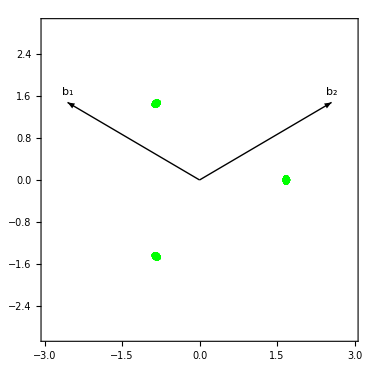

```mathematica
Show[ListPlot[{kaMesh1BZ},AspectRatio->Automatic,Epilog->{lineb1,lineb2,Text["b_1",b1+{0,0.2}],Text["b_2",b2+{0,0.2}]},AspectRatio->Automatic,PlotMarkers->{Graphics[{Green,Disk[{0,0}]}],0.01},PlotStyle->Blue,PlotRange->{{-b,b},{-b,b}},Frame->True], Graphics[{Red,Opacity[0.],EdgeForm [Dashed],BZcontour}] ]
```

-0.049

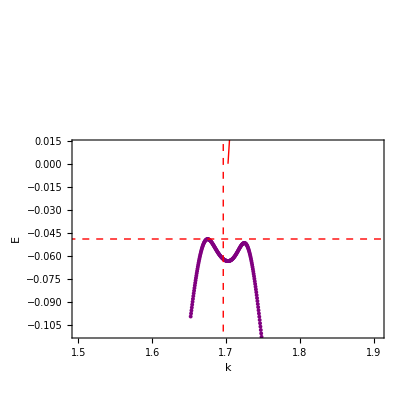

-0.055

```mathematica
Eψk=Map[Eigensystem,Apply[Hk,kaMeshKpoint,{1}]];
Enkp=Eψk[[All,1]];
(*EsurfKp=Flatten[Table[Flatten[{kaMesh1BZ[[i]],Enkp[[i,j]]}],{i,Nk^2},{j,Nb}],1];
ListPointPlot3D[EsurfKp,AspectRatio->1]
ListPlot[{kaMesh1BZ},AspectRatio->Automatic,AspectRatio->Automatic,PlotMarkers->{Graphics[{Green,Disk[{0,0}]}],0.01},PlotStyle->Blue,PlotRange->{{-ba,ba},{-ba,ba}},Frame->True]
*)
iqp=Flatten[Position[kaMeshKpoint ,{kx_,ky_} /; ky==0]];
EpathKp=Flatten[Table[Flatten[{kaMeshKpoint [[iqp[[i]]]][[1]],Enkp[[iqp[[i]],j]]}],{i,Length[iqp]},{j,Nb}],1];
EF=Line[{{-(4π)/(3a),μ},{2*(4π)/(3a),μ}}]; (*Fermi level*)
qF=Line[{{(4π)/(3.*a)+μ/(1*γ0*a),-4*γ0},{(4π)/(3.*a)+μ/(1*γ0*a),4*γ0}}];
Dirac=Line[{{(4π)/(3.*a)+0,0},{(4π)/(3.*a)+1,γ0*a*1}}];
(*To visualize μ better:
δK  = 0.3/a;
δE = 0.02*γ0;
*)
(*Fuller view *)
δK  = 0.5/a;
δE = 0.02*γ0;
k0= (4π)/(3a);
E0=μ

Show[ListPlot[EpathKp,PlotRange->{{k0-δK,k0+δK},{E0-δE,E0+δE}},Joined->False,AspectRatio->1,PlotMarkers->{Automatic, Tiny},PlotStyle->Purple,Frame->True,FrameLabel->{"k","E"}],Graphics[{Red,Dashed,EF}],Graphics[{Red,Dashed,qF}],Graphics[{Red,Thick,Dirac}],Graphics[{Red,Text[{Style["μ=",Medium],μ},{(4π)/(3a),μ+1}]}],Graphics[{Red,Text[{Style["q_F=",Medium],μ/(γ0*a)},{μ/(γ0*a)+1,4*γ0+0.5}]}]]
```

```mathematica
(*Defining parameters for sampling in q*)
Nq=100;
Lq=0.06*4;(*(4π)/(3a)*0.05;*)
Δq=Lq/Nq;

qi=Table[{0.*(-Lq/2)+i*Δq,0.},{i,0,Nq}];
ω=0.;
```

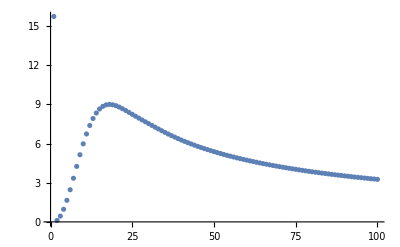

```mathematica
(*Calculating polarizability for q-path*)
Eψk=Map[Eigensystem,Apply[Hk,kaMesh1BZ,{1}]];
Enk=Eψk[[All,1]];
ψnk=Eψk[[All,2]];
ψnk=Map[Normalize,ψnk,{2}];
(*kqaMesh1BZ=kaMesh1BZ; (*Starting with q={0.,0.}*)*)
kqaMesh1BZ=(kaMesh1BZᵀ-0.0*{(4π)/(3a),0})ᵀ;(*Starting to the left of Γ*)
kqaMesh1BZ=kqaMesh1BZ-1*TensorProduct[UnitStep[kqaMesh1BZ[[All,1]]*kqaMesh1BZ[[All,2]]]*Floor[kqaMesh1BZ.b2/b^2+0.5],b2]-1*TensorProduct[(1-UnitStep[kqaMesh1BZ[[All,1]]*kqaMesh1BZ[[All,2]]])*Floor[kqaMesh1BZ.b1/b^2+0.5],b1];

Πq0=Table[0,{i,0,Nq}];
(*The q=0 point:*)
(*
Πq0[[1]] = -(2/Nk^2)*Total[Map[-1/(2*kbT*(1+Cosh[(#-μ)/kbT]))&,Enk],2];
*)
q=0.; (*Used for progress bar only*)
Monitor[
For[i=0,i≤Nq,i++,
q=i*Δq; (*Not being used*)

Eψkq=Map[Eigensystem,Apply[Hk,kqaMesh1BZ,{1}]];
Enkq= Eψkq[[All,1]];
ψnkq=Eψkq[[All,2]];
ψnkq=Map[Normalize,ψnkq,{2}];
(*
nfEk=Map[1/(1+Exp[(#-μ)/kbT])&,Enk];
nfEkq=Map[1/(1+Exp[(#-μ)/kbT])&,Enkq];

nfEk=Map[FDif[#]&,Enk,{2}];
nfEkq=Map[FDif[#]&,Enkq,{2}];
*)
nfEk=Map[UnitStep[μ-#]&,Enk,{2}];
nfEkq=Map[UnitStep[μ-#]&,Enkq,{2}];
(*if ΔE[i]=0., then make ΔE[i]=1., Δnf[i]=δf[i]. To determine which ΔE[i]=0, get indices of elements under threshold, then use those indicies to change Δnf,δf.
Position[Abs[Flatten[ΔE]],_?(# < η &)]*)
Δnf=Flatten[Table[Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,1]]-Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,2]],{i,Nk^2}]];
ΔE=Flatten[Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]]-Tuples[{Enk[[i]],Enkq[[i]]}][[All,2]],{i,Nk^2}]]+ω;(*+ⅈ*η*)
(*δf=Flatten[Map[-1/(2*kbT*(1+Cosh[(#-μ)/kbT]))&,Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]],{i,Nk^2}]]];*)
ψTuples=Table[Tuples[{ψnk[[i]],ψnkq[[i]]*}],{i,Nk^2}];
Fkq=Flatten[Table[Abs[ψTuples[[i]][[j]][[1]].ψTuples[[i]][[j]][[2]]]^2,{i,Nk^2},{j,Nb^2}]];
idiv=Flatten[Position[Abs[ΔE],_?(#==0.&)]];
ΔE[[idiv]]=1.;
(*Fkq[[idiv]]=1.;*)

(*
Δnf[[idiv]]=Map[-1/(2*kbT*(1+Cosh[(#-μ)/kbT]))&,Flatten[Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]],{i,Nk^2}]][[idiv]]];
*)
Δnf[[idiv]]=Map[δFif[#]&,Flatten[Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]],{i,Nk^2}]][[idiv]]];

Πq0[[i+1]]=-(2/Nk^2)*Total[Δnf*Re[1/ΔE]*Fkq];(**((ω)/Norm[q]^2)... -0.*η*Im[1/ΔE]*δf *)
kqaMesh = (kqaMesh1BZᵀ+{Δq,0})ᵀ;

kqaMesh1BZ = kqaMesh-1*TensorProduct[UnitStep[kqaMesh.(b1+b2)]*Floor[kqaMesh.b2/b^2+0.5],b2]-1*TensorProduct[(1-UnitStep[kqaMesh.(b1+b2)])*Floor[kqaMesh.b1/b^2+0.5],b1]
]
,Grid[{{Text[Style["Progress:",Darker[Blue,0.66]]],ProgressIndicator[q,{0.,Lq*1.05}],StringForm["``%",NumberForm[100*q/(Lq*1.05),{3,2}]]},{Text[Style["Current value of q: ",Darker[Blue,0.66]]],q ,StringForm["Final value: ``",NumberForm[Lq]] }},Alignment->Left,Dividers->Center]];
ListPlot[Table[{i,Re[Πq0[[i]]]},{i,1,Nq}]]
```

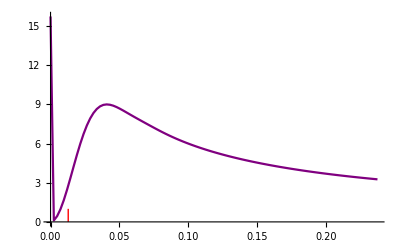

```mathematica
Show[ListPlot[Table[{qi[[i,1]],Re[Πq0[[i]]]},{i,1,Nq}], PlotRange->All,PlotStyle-> Purple,Joined->True],Graphics[{Red,Line[{{-2*μ/(γ0*a),0},{-2*1μ/(γ0*a),1}}]}]]
```

```mathematica
EmitSound[Play[Sin[10*π*t]SawtoothWave[880*2 Pi t],{t,0,0.5}]]
```

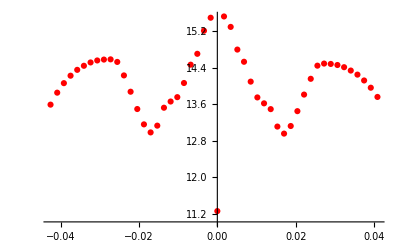

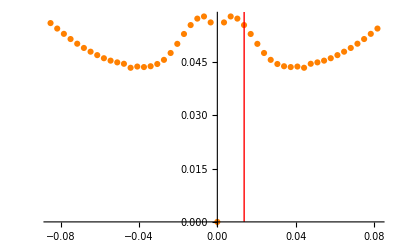
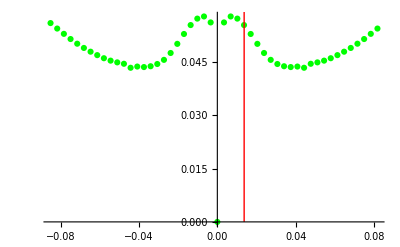
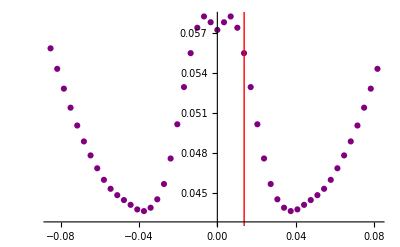
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-](*Before and after flattening before summing over k. Purple: after removing self energy from denominator. We are now subsituting δf for Abs[ΔE]<η, η=0.001,Nk=50*)
```

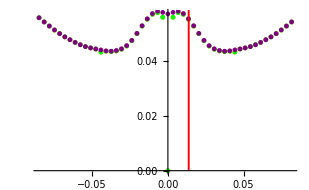

```mathematica
A={1,2,-4,6,8+ⅈ,10};
B=Abs[Re[A]]
B[[{2,5}]]={kk,qq};
B

(*Position[B,_?(#<η&)]*)
```

{1,2,4,6,8,10}

{1,kk,4,6,qq,10}

```mathematica
Enkt={{e1k1,e2k1,e3k1},{e1k2,e2k2,e3k2}};
Enkqt={{e1q1,e2q1,e3q1},{e1q2,e2q2,e3q2}};
i=2;
Tuples[{Enkt[[i]],Enkqt[[i]]}][[All,1]][[{1,4,7}]]
Tuples[{Enkt[[i]],Enkqt[[i]]}][[All,1]]-Tuples[{Enkt[[i]],Enkqt[[i]]}][[All,2]]
```

{e1k2,e2k2,e3k2}

{e1k2-e1q2,e1k2-e2q2,e1k2-e3q2,-e1q2+e2k2,e2k2-e2q2,e2k2-e3q2,-e1q2+e3k2,-e2q2+e3k2,e3k2-e3q2}

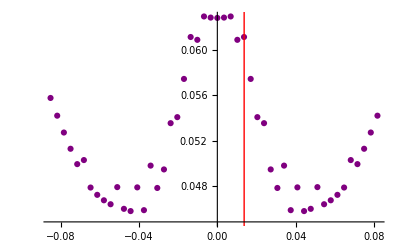
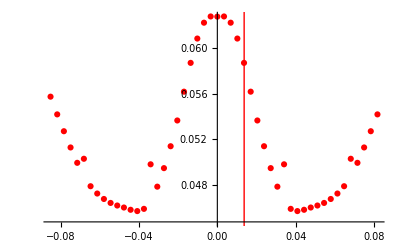
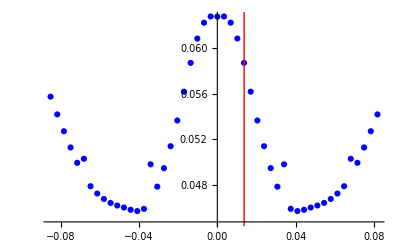
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-](*Purple: Same but for Nk=150. Red: Same but η=0.0001, this fixed the points closer to q=0*)
```

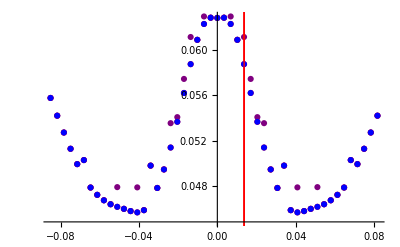

```mathematica
(*Started at pm 5/3/21*)(*calcualting same resolution but for the main cuadrant ω,q<1.25*)(**)
Monitor[Table[Pause[0.001],{ω,0.625,1.25,(1.25-0.625)/20},{q,0.01,0.625,(0.625-0.01)/20}],Grid[{{Text[Style["Progress:",Darker[Blue,0.66]]],ProgressIndicator[ω,{0.625,1.25}],StringForm["``%",NumberForm[100*(ω-0.625)/(1.25-0.625),{3,2}]]},{Text[Style["Current value of ω: ",Darker[Blue,0.66]]],ω ,StringForm["Final value: ``",NumberForm[1.25]] }},Alignment->Left,Dividers->Center]];
```

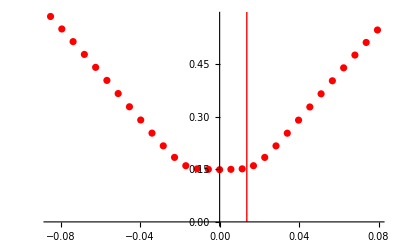
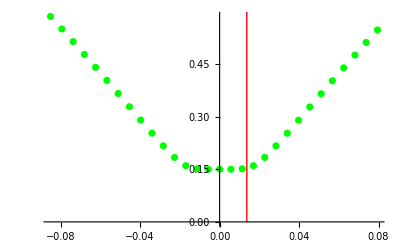
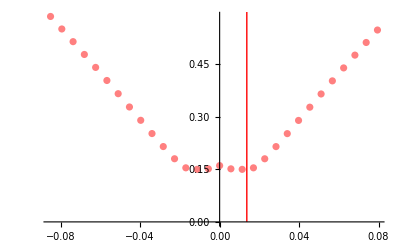
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-] (*Nk=150, kamesh*0.2, K-centered, graphene parameters. Div condition # < 0. fixed problems at q=0,q_\pm. Removed Fkq=1. it didn.b4t appear to make difference.Green: Nk=200, almost no diff., a little diff at q=0. Pink: kbT=0.05 mK (the other ones are at 0.1mK), looks flatter but seems to diverge at q=0 *)
```

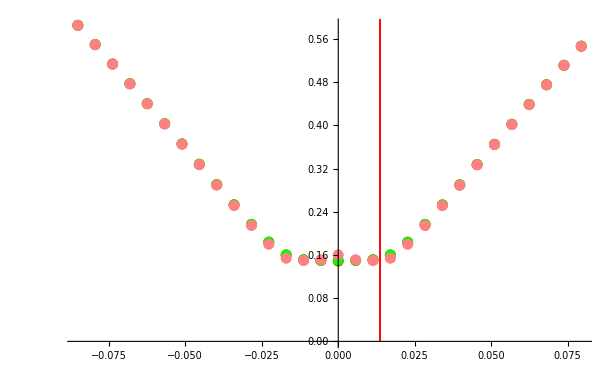

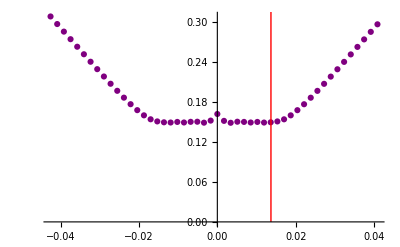
```mathematica
Show[-Graphics-](*Same but Nq=50, Lq=(4π)/(3a)*0.05*)
```

-Graphics-

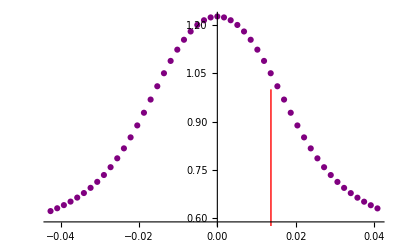
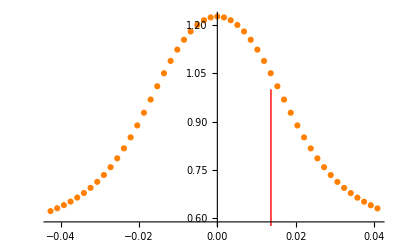
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-](*Same but for trilayer parameters, for Nk=200. Green: Nk=300 (didn't change). Yellow: kamesh*0.05. Nk=200 (didn't change), Orange: kamesh*0.2 (didnt change)*)
```

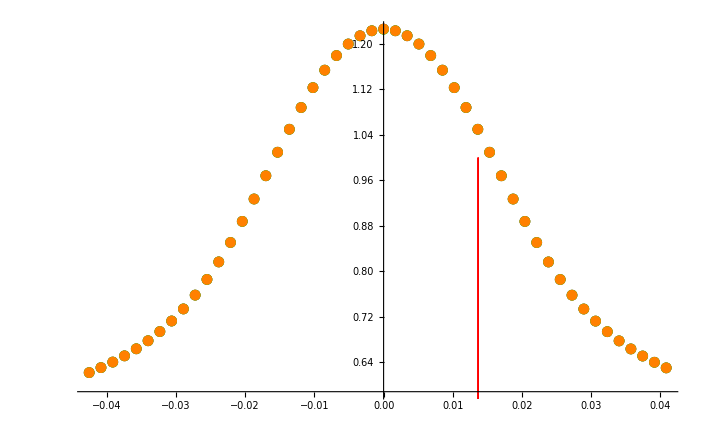

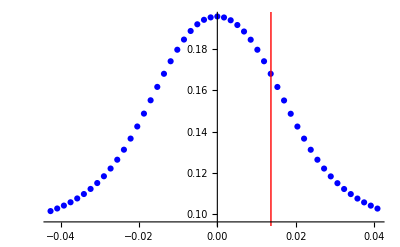
```mathematica
Show[-Graphics-](*Blue: kamesh*0.5, THE AMPLITUDE CHANGES A LOT*)
```

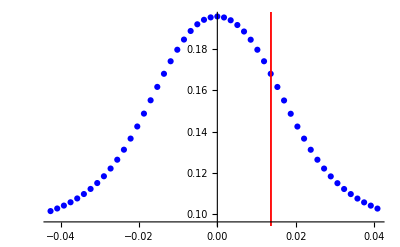

-Graphics-

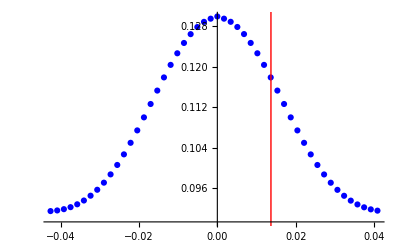
```mathematica
Show[-Graphics-] (*Green: T= 0.1mK (past plots were  at 0.05mk)*)
```

-Graphics-

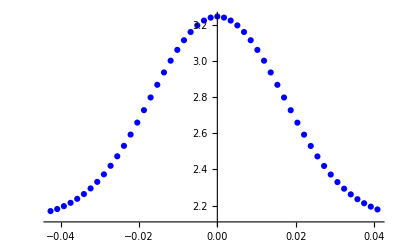
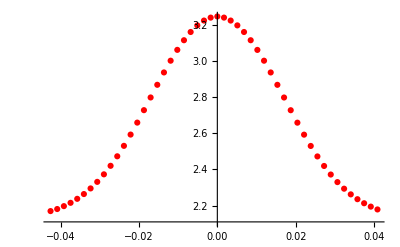
```mathematica
Show[-Graphics-,-Graphics-](*TESTING CUT FOR FD[ϵk].For Nk=50. Blue: before, Red: after. Seems to not have changed*)
```

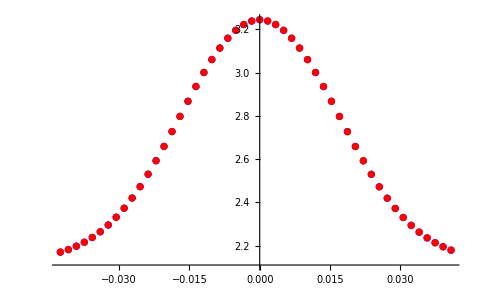

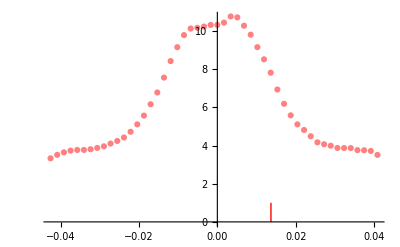
```mathematica
Show[-Graphics-] (*For T=0.01mk*)
```

-Graphics-

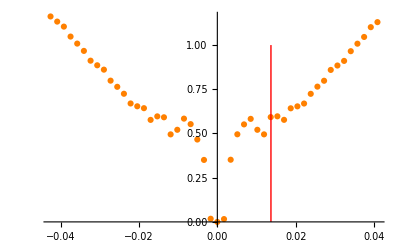
```mathematica
Show[-Graphics-] (*Graphene parameters. Nk=50, kamesh*0.05, K-centered, cut fermi distributions. T=0.01mK (now there are no errors of exponentials)*)
```

-Graphics-

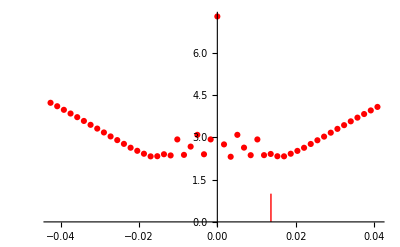
```mathematica
Show[-Graphics-](*Same but kamesh*0.05 (it got better!)*)
```

-Graphics-

```mathematica
Show[-Graphics-] (*Same but kamesh*0.02 (it got worse!)*)
```

-Graphics-

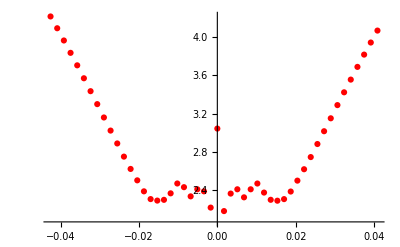
```mathematica
Show[-Graphics-](*Same but Nk=100*)
```

-Graphics-

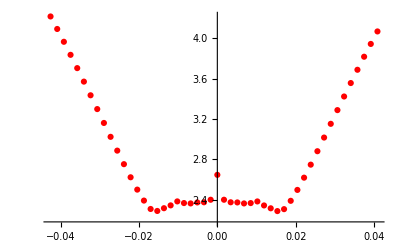
```mathematica
Show[-Graphics-] (*Nk=150*)
```

-Graphics-

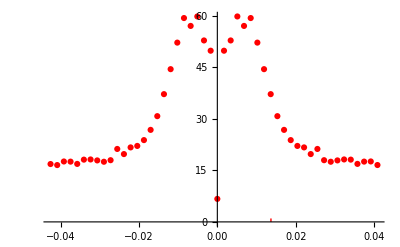
```mathematica
Show[-Graphics-](*Trilayer parameters, Nk=150, replacing FD by  UnitStep*)
```

-Graphics-

```mathematica
Show[-Graphics-](*Nk=150*)
```

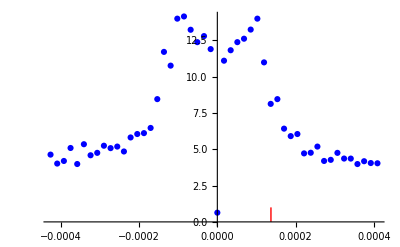
```mathematica
Show[-Graphics-](*a->s*a, s=100, T=5K*)
```

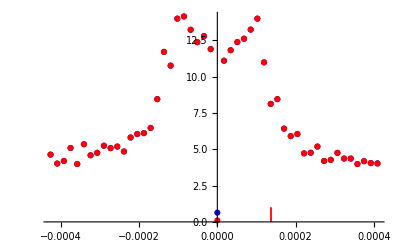

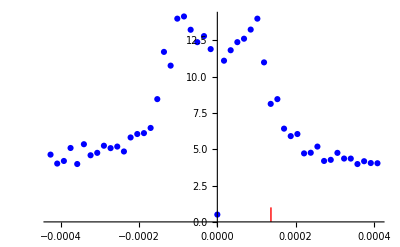
```mathematica
Show[-Graphics-](*T=10K*)
```

-Graphics-

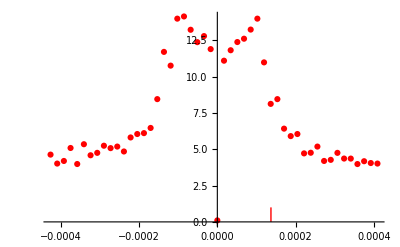
```mathematica
Show[-Graphics-] (*T=100K. Its not changing*)
```

-Graphics-

```mathematica
N[12*10^4]
```

120000.

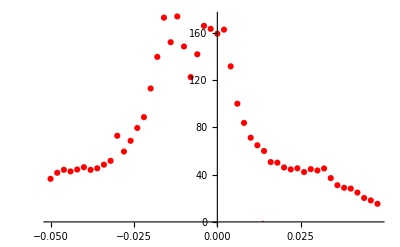
```mathematica
Show[-Graphics-] (*Trying to reproduce the results of Simplified model with realistic parameters. Nk=100, T=100K, kamesh*0.03, Lq=0.1, Nq= 50, μ=-0.052175, δc=10.*kbT. (my mistake, I didn't center on q, but maybe this is acually more accurate than I thought)*)
```

-Graphics-

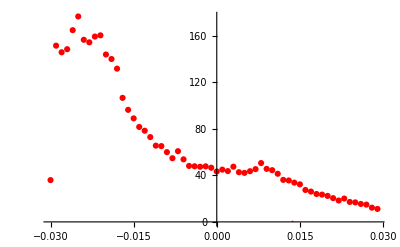
```mathematica
Show[-Graphics-] (*Nq=60, Starting at K point (instead of going through it from K-Lq/2 to K+Lq/2). Also Lq=0.06*)
```

-Graphics-

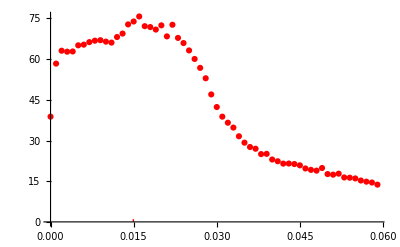
```mathematica
Show[-Graphics-] (*Same but μ=-0.57, also fixed the starting point of q path at K*)
```

-Graphics-

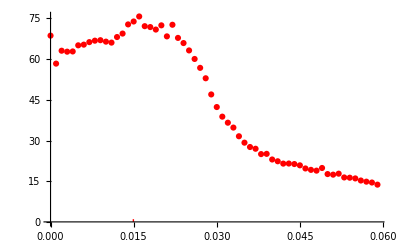
```mathematica
Show[-Graphics-] (*Same but T=10K*)
```

-Graphics-

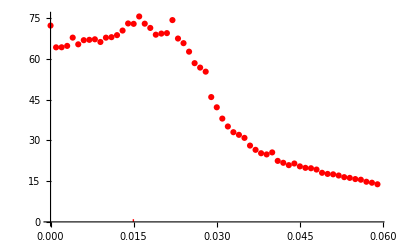
```mathematica
Show[-Graphics-] (*Same but T=1K, Nk=150. You kind of see the 3 expected peaks, 2 around 0.02 and 1 around 0.4. The ones at low q is probably noise due to low Nk,as we've seen from the simplified model*)
```

-Graphics-

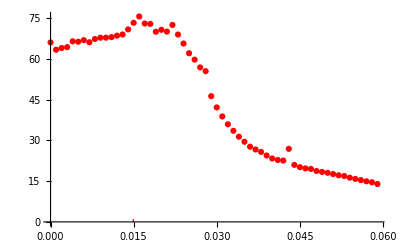
```mathematica
Show[-Graphics-](*Same but Nk=250*)
```

-Graphics-

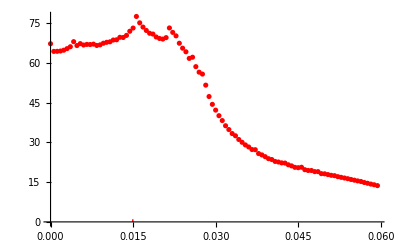
```mathematica
Show[-Graphics-] (*Same but Nk=300, Nq=100*)
```

-Graphics-

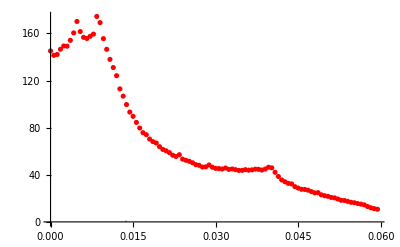
```mathematica
Show[-Graphics-] (*Same but μ at VHS*)
```

-Graphics-

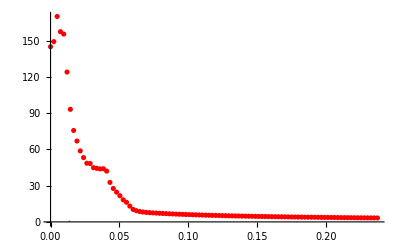
```mathematica
Show[-Graphics-](*Same but Nq=100, Lq=0.06*4*)
```

-Graphics-

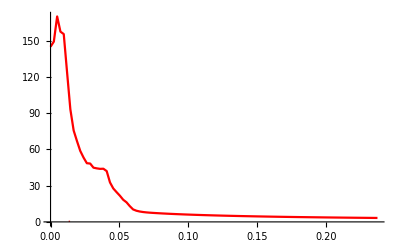
```mathematica
(*DATA*)
Show[-Graphics-]
Table[{qi[[i,1]],Re[Πq0[[i]]]},{i,1,Nq}]
```

-Graphics-

```mathematica
dataμVHS={{0.,145.06150868045785},{0.0024,149.3145748542893},{0.0048,170.12791011599455},{0.0072,157.53864460655166},{0.0096,155.53907893878136},{0.011999999999999999,124.09592502686013},{0.0144,93.2193081325244},{0.0168,75.70931583370641},{0.0192,66.9695816428422},{0.021599999999999998,58.777758258296586},{0.023999999999999997,53.24571264744643},{0.026399999999999996,48.59839464113396},{0.0288,48.32422747499152},{0.0312,44.90516760576428},{0.0336,44.3331614198124},{0.036,43.92578613051369},{0.0384,44.02183827099721},{0.040799999999999996,42.078526434143384},{0.043199999999999995,32.70449393497308},{0.045599999999999995,27.686925118849388},{0.047999999999999994,24.62042127339301},{0.05039999999999999,21.689857735960224},{0.05279999999999999,18.340295406859912},{0.05519999999999999,16.237877371532896},{0.0576,13.05338425628327},{0.06,10.333919125716658},{0.0624,9.249079339962742},{0.0648,8.60684868296063},{0.0672,8.178338289876734},{0.0696,7.874964066887173},{0.072,7.644736007443611},{0.0744,7.456811068717207},{0.0768,7.288442965105074},{0.07919999999999999,7.130784987748473},{0.08159999999999999,6.982079191926833},{0.08399999999999999,6.841353566235895},{0.08639999999999999,6.707869185366134},{0.08879999999999999,6.580992659334931},{0.09119999999999999,6.460156583095777},{0.09359999999999999,6.34484966721123},{0.09599999999999999,6.234613795238058},{0.09839999999999999,6.129041117706454},{0.10079999999999999,6.027770002457274},{0.10319999999999999,5.930480231082339},{0.10559999999999999,5.8368880140015085},{0.10799999999999998,5.746741229771648},{0.11039999999999998,5.659815105339867},{0.11279999999999998,5.575908419330679},{0.1152,5.4948402304927475},{0.1176,5.416447092261594},{0.12,5.340580697146245},{0.1224,5.267105890839125},{0.1248,5.195898999009128},{0.12719999999999998,5.126846415830821},{0.1296,5.059843410318701},{0.13199999999999998,4.994793113393265},{0.1344,4.9316056548110065},{0.13679999999999998,4.870197424468516},{0.1392,4.810490437132281},{0.14159999999999998,4.752411783418172},{0.144,4.695893152945977},{0.14639999999999997,4.640870418127467},{0.1488,4.5872832691081395},{0.15119999999999997,4.5350748920574535},{0.1536,4.484191684362294},{0.156,4.434583001383518},{0.15839999999999999,4.386200930334816},{0.1608,4.339000087576499},{0.16319999999999998,4.292937436216547},{0.1656,4.247972121402869},{0.16799999999999998,4.204065321095391},{0.1704,4.1611801104402755},{0.17279999999999998,4.119281338145391},{0.1752,4.078335513486054},{0.17759999999999998,4.03831070276209},{0.18,3.9991764341881493},{0.18239999999999998,3.960903610334471},{0.1848,3.9234644273497774},{0.18719999999999998,3.886832300294646},{0.1896,3.850981793996346},{0.19199999999999998,3.8158885589066185},{0.1944,3.7815292715042133},{0.19679999999999997,3.747881578836165},{0.1992,3.7149240468366798},{0.20159999999999997,3.682636112101591},{0.204,3.650998036830225},{0.20639999999999997,3.6199908666761553},{0.20879999999999999,3.589596391274378},{0.21119999999999997,3.5597971072351884},{0.21359999999999998,3.530576183415224},{0.21599999999999997,3.5019174282938677},{0.21839999999999998,3.4738052592991413},{0.22079999999999997,3.4462246739410887},{0.22319999999999998,3.419161222623316},{0.22559999999999997,3.392600983014422},{0.22799999999999998,3.3665305358712794},{0.2304,3.3409369422149044},{0.23279999999999998,3.315807721767979},{0.2352,3.2911308325702864},{0.23759999999999998,3.2668946516950346}};
```

```mathematica
Show[-Graphics-] (*Same but μ=-0.51*)
```

-Graphics-

```mathematica
dataμmp051={{0.,104.27401177717853},{0.0024,101.51843137880641},{0.0048,93.48261823763929},{0.0072,89.58018555909207},{0.0096,78.74409940717767},{0.011999999999999999,62.37101388078931},{0.0144,55.82481091098878},{0.0168,49.5535302543704},{0.0192,39.890677888184335},{0.021599999999999998,33.6169774253293},{0.023999999999999997,30.2071293383437},{0.026399999999999996,27.55624417865824},{0.0288,26.00284450372653},{0.0312,24.92911102418544},{0.0336,23.93974294802603},{0.036,23.08811084030795},{0.0384,22.170082213062127},{0.040799999999999996,21.964230115211404},{0.043199999999999995,24.913619435483497},{0.045599999999999995,24.18729222000184},{0.047999999999999994,20.349108415756355},{0.05039999999999999,16.746125522289336},{0.05279999999999999,13.600674344111525},{0.05519999999999999,10.967759380222313},{0.0576,9.482854241900139},{0.06,8.742344576883585},{0.0624,8.30230483419254},{0.0648,8.021972804949367},{0.0672,7.814858217895172},{0.0696,7.635000058018363},{0.072,7.470372732680273},{0.0744,7.3152964098949855},{0.0768,7.167281296779751},{0.07919999999999999,7.025383725035804},{0.08159999999999999,6.889286556813479},{0.08399999999999999,6.758834307354408},{0.08639999999999999,6.633851714175518},{0.08879999999999999,6.514105722379532},{0.09119999999999999,6.399320211382063},{0.09359999999999999,6.289200294069597},{0.09599999999999999,6.183451580565573},{0.09839999999999999,6.081792104722993},{0.10079999999999999,5.983958420514692},{0.10319999999999999,5.889707885931961},{0.10559999999999999,5.798818722208346},{0.10799999999999998,5.711088903642936},{0.11039999999999998,5.626334520036027},{0.11279999999999998,5.544387977970089},{0.1152,5.465096236414608},{0.1176,5.388319171393374},{0.12,5.313928107404647},{0.1224,5.241804522443887},{0.1248,5.1718389178992625},{0.12719999999999998,5.1039298376497095},{0.1296,5.0379830184804675},{0.13199999999999998,4.973910654171998},{0.1344,4.911630757027936},{0.13679999999999998,4.8510666024736135},{0.1392,4.792146244300584},{0.14159999999999998,4.734802089966548},{0.144,4.678970527002071},{0.14639999999999997,4.624591593001209},{0.1488,4.57160868288777},{0.15119999999999997,4.519968288171153},{0.1536,4.469619763759641},{0.156,4.420515118608732},{0.15839999999999999,4.372608827071342},{0.1608,4.325857658304482},{0.16319999999999998,4.280220521491858},{0.1656,4.235658324977555},{0.16799999999999998,4.192133847685525},{0.1704,4.149611621432196},{0.17279999999999998,4.1080578229343825},{0.1752,4.067440174477901},{0.17759999999999998,4.027727852349505},{0.18,3.9888914022509927},{0.18239999999999998,3.9509026610124174},{0.1848,3.9137346840050733},{0.18719999999999998,3.8773616777263675},{0.1896,3.8417589370897907},{0.19199999999999998,3.80690278700602},{0.1944,3.7727705278865766},{0.19679999999999997,3.7393403847409674},{0.1992,3.7065914595725915},{0.20159999999999997,3.6745036868085905},{0.204,3.643057791525193},{0.20639999999999997,3.6122352502531583},{0.20879999999999999,3.5820182541682812},{0.21119999999999997,3.5523896744900747},{0.21359999999999998,3.523333029927589},{0.21599999999999997,3.494832456025768},{0.21839999999999998,3.466872676278326},{0.22079999999999997,3.4394389748846357},{0.22319999999999998,3.412517171038271},{0.22559999999999997,3.386093594644075},{0.22799999999999998,3.3601550633689863},{0.2304,3.334688860939212},{0.23279999999999998,3.3096827166033},{0.2352,3.2851247856867016},{0.23759999999999998,3.2610036311690807}};
```

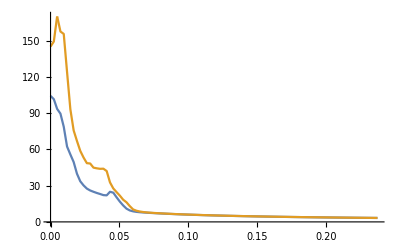

```mathematica
ListPlot[{dataμmp051,dataμVHS},Joined->True,PlotRange->{0,170}]
```

```mathematica
dataμmp05={{0.,74.25586575814395},{0.0024,72.75691903706496},{0.0048,70.28961832490111},{0.0072,59.38862926320512},{0.0096,50.809962759090176},{0.011999999999999999,31.944452658646316},{0.0144,24.05250152077733},{0.0168,20.4772954776708},{0.0192,17.983798617434356},{0.021599999999999998,16.444410143481246},{0.023999999999999997,15.306997710699259},{0.026399999999999996,14.107187470811448},{0.0288,13.245913722764152},{0.0312,12.516999749247132},{0.0336,11.892262583237253},{0.036,11.457616734206379},{0.0384,11.32160743543161},{0.040799999999999996,11.385606191071613},{0.043199999999999995,11.7379059296005},{0.045599999999999995,12.373595086871942},{0.047999999999999994,12.536116451859327},{0.05039999999999999,11.621425847695898},{0.05279999999999999,10.284718776228338},{0.05519999999999999,9.238855721084315},{0.0576,8.639007301159786},{0.06,8.29672961159915},{0.0624,8.065138685374851},{0.0648,7.878513951406936},{0.0672,7.713670329924615},{0.0696,7.560000534042955},{0.072,7.412533651384371},{0.0744,7.269216795429947},{0.0768,7.129563461735022},{0.07919999999999999,6.993800723435167},{0.08159999999999999,6.862327701832635},{0.08399999999999999,6.735444148860854},{0.08639999999999999,6.6132736720406555},{0.08879999999999999,6.495785010580962},{0.09119999999999999,6.382841689874258},{0.09359999999999999,6.274247598553646},{0.09599999999999999,6.1697795992696935},{0.09839999999999999,6.069208045970163},{0.10079999999999999,5.972308538140602},{0.10319999999999999,5.878868008597806},{0.10559999999999999,5.7886873883766885},{0.10799999999999998,5.701582312088866},{0.11039999999999998,5.617382765275733},{0.11279999999999998,5.535932208262065},{0.1152,5.457086483065076},{0.1176,5.380712672629904},{0.12,5.306688000855324},{0.1224,5.2348988153358595},{0.1248,5.165239668640945},{0.12719999999999998,5.0976124998549865},{0.1296,5.0319259109580745},{0.13199999999999998,4.96809452943234},{0.1344,4.906038447466213},{0.13679999999999998,4.845682728268533},{0.1392,4.786956970705904},{0.14159999999999998,4.729794924407799},{0.144,4.674134148463905},{0.14639999999999997,4.619915707774331},{0.1488,4.567083901962975},{0.15119999999999997,4.515586022512181},{0.1536,4.465372134423264},{0.156,4.416394879258909},{0.15839999999999999,4.368609296891182},{0.1608,4.321972663672946},{0.16319999999999998,4.276444345082313},{0.1656,4.231985661168523},{0.16799999999999998,4.18855976336233},{0.1704,4.146131521411121},{0.17279999999999998,4.10466741936574},{0.1752,4.064135459686574},{0.17759999999999998,4.024505074655767},{0.18,3.9857470443839027},{0.18239999999999998,3.9478334207859085},{0.1848,3.9107374569749784},{0.18719999999999998,3.874433541586908},{0.1896,3.838897137601909},{0.19199999999999998,3.8041047252784317},{0.1944,3.770033748854573},{0.19679999999999997,3.7366625667084397},{0.1992,3.703970404700212},{0.20159999999999997,3.671937312445953},{0.204,3.64054412229749},{0.20639999999999997,3.6097724108239193},{0.20879999999999999,3.5796044626091494},{0.21119999999999997,3.5500232361967496},{0.21359999999999998,3.521012332028166},{0.21599999999999997,3.4925559622337996},{0.21839999999999998,3.46463892214832},{0.22079999999999997,3.4372465634323457},{0.22319999999999998,3.410364768692254},{0.22559999999999997,3.3839799274985163},{0.22799999999999998,3.3580789137110085},{0.2304,3.3326490640266044},{0.23279999999999998,3.307678157671085},{0.2352,3.283154397163093},{0.23759999999999998,3.259066390083339}};
```

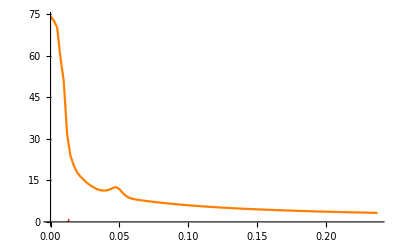
```mathematica
Show[-Graphics-](*Same but μ=-0.05*)
```

-Graphics-

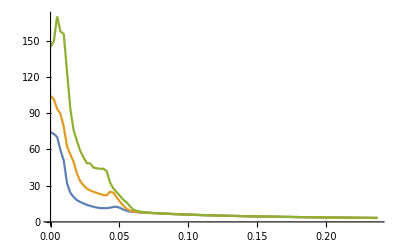

```mathematica
ListPlot[{dataμmp05,dataμmp051,dataμVHS},Joined->True,PlotRange->{0,170}]
```

```mathematica
Show[-Graphics-] (*Same but μ=-0.049*)
```

-Graphics-

```mathematica
dataμmp049={{0.,15.723842749269235},{0.0024,0.11230852940809548},{0.0048,0.4418446794761522},{0.0072,0.966878422913029},{0.0096,1.6537434741461774},{0.011999999999999999,2.4604570978121925},{0.0144,3.3407465542427124},{0.0168,4.247976728512669},{0.0192,5.138670854101364},{0.021599999999999998,5.975420458889489},{0.023999999999999997,6.728965226013326},{0.026399999999999996,7.379232327542138},{0.0288,7.915295694257895},{0.0312,8.33446545648909},{0.0336,8.640848295386345},{0.036,8.84368491834052},{0.0384,8.95567488034477},{0.040799999999999996,8.991422362199703},{0.043199999999999995,8.966087998951444},{0.045599999999999995,8.894296478090027},{0.047999999999999994,8.789319167329333},{0.05039999999999999,8.662524673418302},{0.05279999999999999,8.52307051925499},{0.05519999999999999,8.37780007054213},{0.0576,8.231312988791238},{0.06,8.086191260066398},{0.0624,7.943374210038833},{0.0648,7.802668691606096},{0.0672,7.663345302102296},{0.0696,7.524717320404241},{0.072,7.386559870222845},{0.0744,7.249250084855197},{0.0768,7.113617755688016},{0.07919999999999999,6.98063720481671},{0.08159999999999999,6.851148856594987},{0.08399999999999999,6.725722033138798},{0.08639999999999999,6.604649900613404},{0.08879999999999999,6.488010631170913},{0.09119999999999999,6.375740017854183},{0.09359999999999999,6.2676906735044025},{0.09599999999999999,6.163672940710258},{0.09839999999999999,6.063480586263242},{0.10079999999999999,5.9669058541044295},{0.10319999999999999,5.873747695485304},{0.10559999999999999,5.7838158496220125},{0.10799999999999998,5.69693249966195},{0.11039999999999998,5.612932567749806},{0.11279999999999998,5.531663286260182},{0.1152,5.452983417666641},{0.1176,5.376762335335616},{0.12,5.302879082183661},{0.1224,5.231221468222038},{0.1248,5.161685235775888},{0.12719999999999998,5.094173303006864},{0.1296,5.028595086501023},{0.13199999999999998,4.964865898642095},{0.1344,4.902906413211772},{0.13679999999999998,4.842642191922056},{0.1392,4.78400326467349},{0.14159999999999998,4.726923756832406},{0.144,4.671341557492895},{0.14639999999999997,4.617198023405106},{0.1488,4.564437713941882},{0.15119999999999997,4.513008153107629},{0.1536,4.462859615154761},{0.156,4.41394493086169},{0.15839999999999999,4.366219311947415},{0.1608,4.319640191456881},{0.16319999999999998,4.27416707825686},{0.1656,4.229761424040916},{0.16799999999999998,4.186386501461586},{0.1704,4.144007292193363},{0.17279999999999998,4.102590383887906},{0.1752,4.062103875116496},{0.17759999999999998,4.0225172875086885},{0.18,3.9838014843932905},{0.18239999999999998,3.9459285953309244},{0.1848,3.9088719459987624},{0.18719999999999998,3.872605992949566},{0.1896,3.8371062628201056},{0.19199999999999998,3.8023492956101554},{0.1944,3.7683125916932037},{0.19679999999999997,3.7349745622549335},{0.1992,3.7023144828861363},{0.20159999999999997,3.670312450083453},{0.204,3.6389493404351385},{0.20639999999999997,3.6082067722897864},{0.20879999999999999,3.578067069724589},{0.21119999999999997,3.5485132286461565},{0.21359999999999998,3.51952888487154},{0.21599999999999997,3.4910982840503397},{0.21839999999999998,3.4632062533004455},{0.22079999999999997,3.4358381744405944},{0.22319999999999998,3.408979958712418},{0.22559999999999997,3.38261802289323},{0.22799999999999998,3.3567392667086695},{0.2304,3.331331051461197},{0.23279999999999998,3.3063811797970217},{0.2352,3.281877876539712},{0.23759999999999998,3.257809770524149}};
```

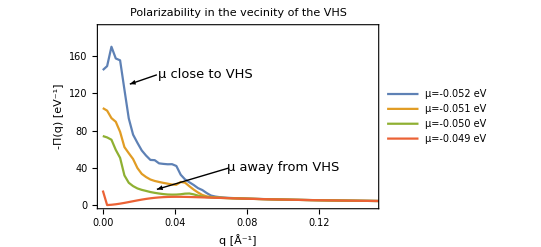

```mathematica
ListPlot[{dataμVHS,dataμmp051,dataμmp05,dataμmp049},Joined->True,PlotRange->{{0,.15},{0,190}},PlotLegends->{"μ=-0.052 eV","μ=-0.051 eV","μ=-0.050 eV","μ=-0.049 eV"},Frame-> True, FrameLabel->{"q [Å^-1]",-"Π(q) [eV^-1]"},LabelStyle->Directive[Black,20,FontFamily->"Times"],Epilog->{Arrow[{{.03,140},{0.015,130}}],Inset[Style["μ close to VHS",13],{0.057,140}](*,Arrow[{{.05,60},{0.025,35}}],Arrow[{{.05,50},{0.02,20}}]*),Inset[Style["μ away from VHS",13],{0.1,40}],Arrow[{{.07,40},{0.03,17}}]},PlotLabel->Style["Polarizability in the vecinity of the VHS"]]
```

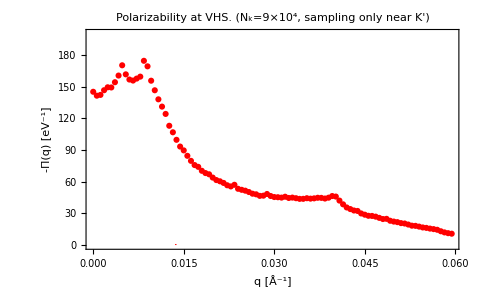

```mathematica
Show[-Graphics-,Frame-> True, FrameLabel->{"q [Å^-1]",-"Π(q) [eV^-1]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotRange->{0,200},PlotLabel->Style["Polarizability at VHS. (N_k=9×10^4, sampling only near K')"]]
```

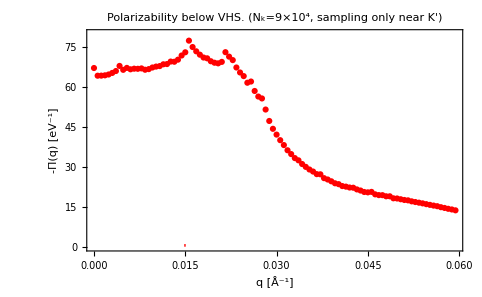

```mathematica
Show[-Graphics-,Frame-> True, FrameLabel->{"q [Å^-1]",-"Π(q) [eV^-1]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotRange->{0,80},PlotLabel->Style["Polarizability below VHS. (N_k=9×10^4, sampling only near K')"]]
```